Adapted from http://demonstrations.wolfram.com/MolecularDynamicsOfLennardJonesParticlesUsingTheVelocityVerl/

```mathematica
ClearAll["Global`*"]
SeedRandom[]
```

```mathematica
(* use natural units *)
ϵ=1.0;
σ=1.0;
m=1.0;
dt=0.002σ*Sqrt[m/ϵ];
```

```mathematica
pairForce:=
Function[{ii,jj,posk},
Module[{xii,xjj,r,vector,r6},
xii=posk[[ii,All]];
xjj=posk[[jj,All]];
r=Sqrt[(xjj[[1]]-xii[[1]])^2+(xjj[[2]]-xii[[2]])^2+(xjj[[3]]-xii[[3]])^2];
vector=(xii- xjj)/r;
(* Use this trick avoids enormous forces when particles get (artificially) too close. Therefore this is a modified Lennard-Jones Force:  r=Max[r,σ];*)
r6 = r^6;
4*ϵ*(12σ^12/(r6^2*r)-6σ^6/(r6*r))*vector ] ]

pairEnergy:=
Function[{ii,jj,posk},
Module[{xii,xjj,r,vector,r6},
xii=posk[[ii,All]];
xjj=posk[[jj,All]];
r=Sqrt[(xjj[[1]]-xii[[1]])^2+(xjj[[2]]-xii[[2]])^2+(xjj[[3]]-xii[[3]])^2];
(* Use this trick avoids enormous forces when particles get (artificially) too close. Therefore this is a modified Lennard-Jones Force:  r=Max[r,σ];*)
r6 = r^6;
4*ϵ*(σ^12/r6^2-σ^6/r6) ] ]

pairForceSum:=Function[{posk},
Module[{nat,forceTable,forcesum},
nat=Dimensions[posk][[1]];
forceTable=Table[{0.0,0.0,0.0},{i,1,nat},{j,1,nat}];
Do[forceTable[[i,j]]=pairForce[i,j,posk[[All,All]] ],{i,2,nat},{j,1,i-1}];Do[forceTable[[i,j]]=pairForce[i,j,posk[[All,All]] ],{i,1,nat-1},{j,i+1,nat}];
forcesum=Sum[forceTable[[All,i]],{i,1,nat}]
  ] ]

pairEnergySum:=Function[{posk},
Module[{nat,energysum},
nat=Dimensions[posk][[1]];
Sum[Sum[pairEnergy[i,j,posk ],{j,1,i-1}],{i,2,nat}]
  ] ]
```

```mathematica
(* define table sizes andinitialize tables with zeroes , storing all steps *)
natoms=13;
timesteps = 2000;(*alterado de 1000 para 500*)
position = Table[0.0,{k,1,timesteps+1},{j,1,natoms},{i,1,3}];velocity = Table[0.0,{k,1,timesteps+1},{j,1,natoms},{i,1,3}];
force=Table[0.0,{k,1,timesteps+1},{j,1,natoms},{i,1,3}];
energy = Table[0.0,{k,1,timesteps+1}];
kinetic = Table[0.0,{k,1,timesteps+1}];
```

```mathematica
(* initialize positions to 13 atom cubo-octahedron*)
dfcc = 1.0/(√2.0) 2.0^(1/6) σ;
position[[1,1,1]]=0.1 dfcc(*0.1*);
position[[1,1,2]]=-0.1 dfcc(*-0.1*);
position[[1,1,3]]=-0.05 dfcc(*-0.05*);

position[[1,2,1]]=0.0;
position[[1,2,2]]=dfcc;
position[[1,2,3]]=dfcc;

position[[1,3,1]]=dfcc;
position[[1,3,2]]=0.0;
position[[1,3,3]]=dfcc;

position[[1,4,1]]= dfcc;
position[[1,4,2]]=dfcc;
position[[1,4,3]]=0;

position[[1,5,1]]=0.0;
position[[1,5,2]]=-dfcc;
position[[1,5,3]]=dfcc;

position[[1,6,1]]=-dfcc;
position[[1,6,2]]=0.0;
position[[1,6,3]]=dfcc;

position[[1,7,1]]=-dfcc;
position[[1,7,2]]=dfcc;
position[[1,7,3]]=0.0;

position[[1,8,1]]=0.0;
position[[1,8,2]]=dfcc;
position[[1,8,3]]=-dfcc;

position[[1,9,1]]=dfcc;
position[[1,9,2]]=0.0;
position[[1,9,3]]=-dfcc;

position[[1,10,1]]=dfcc;
position[[1,10,2]]=-dfcc;
position[[1,10,3]]=0.0;

position[[1,11,1]]=0.0;
position[[1,11,2]]=-dfcc;
position[[1,11,3]]=-dfcc;

position[[1,12,1]]=-dfcc;
position[[1,12,2]]=0.0;
position[[1,12,3]]=-dfcc;
(*quebra de simetria*)
position[[1,13,1]]=4/3 dfcc;(*-*)
position[[1,13,2]]=4/3 dfcc;(*-*)
position[[1,13,3]]=4/3 dfcc;
```

```mathematica
(* Plot of the first configuration *)
ListPointPlot3D[ position[[1,All,All]] ,BoxRatios->{1, 1, 1} ,PlotStyle->{PointSize[0.1]},PlotRangePadding->0.3,Axes->None]
```

-Graphics3D-

```mathematica
(* Initialize velocities (by default they are zero) and calculate kinetic energy *)
Do[Do[velocity[[1,j,i]]=0.05RandomReal[],{i,1,3}],{j,1,13}]

Do[force[[k,All,All]]=pairForceSum[ position[[k,All,All]] ];    energy[[k]] =pairEnergySum[ position[[k,All,All]]  ] ;kinetic[[k]] = 0.5  m  Sum[velocity[[k,j,i]]^2,{j,1,natoms},{i,1,3}];

(*Verlet Integration*)

If[k==1,position[[k+1,All,All]]=position[[k,All,All]]+dt velocity[[k,All,All]]+1/2 dt^2/m force[[k,All,All]]];
If[k≠1,position[[k+1,All,All]]=2 position[[k,All,All]]-position[[k-1,All,All]]+dt^2/m force[[k,All,All]];velocity[[k,All,All]]=(position[[k+1,All,All]]-position[[k-1,All,All]])/(2 dt)],{k,1,timesteps}]




energy[[timesteps+1]] =pairEnergySum[ position[[timesteps+1,All,All]]  ] ;
kinetic[[timesteps+1]] = 0.5  m  Sum[velocity[[timesteps+1,j,i]]^2,{j,1,natoms},{i,1,3}];
force[[timesteps+1,All,All]]=pairForceSum[ position[[timesteps+1,All,All]] ];
```

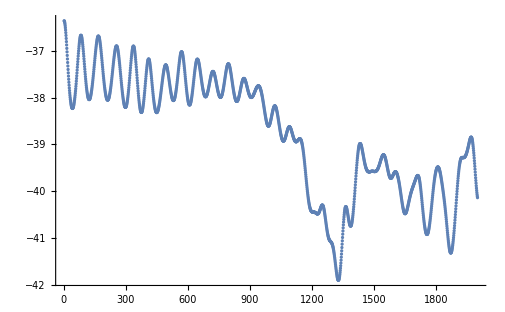

```mathematica
ListPlot[energy,PlotRange->All]
```

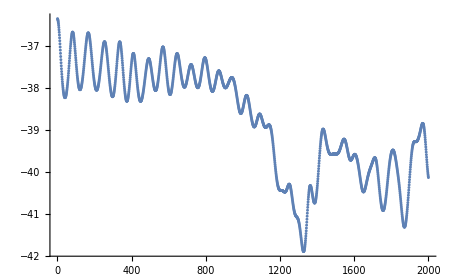

```mathematica
ListPlot[energy+kinetic,PlotRange->All]
```

```mathematica
Animate[ListPointPlot3D[ position[[i,All,All]] ,BoxRatios->{1, 1, 1} ,PlotRange->All,PlotStyle->{PointSize[0.1]},PlotRangePadding->0.3,Axes->None,Boxed->False],{i,1,timesteps,1}]
```

```mathematica
(*natural units*)
kb=1
```

1

```mathematica
averageKE=Sum[ dt kinetic[[i]],{i,1,timesteps}]/Sum[dt,{i,1,timesteps}]
```

6.04149×10^-6

```mathematica
Solve[averageKE==3/2 natoms kb T,T]
```

{{T→3.0982×10^-7}}

### Para aquecer ou arrefecer o sistema, basta mudar a constatnte C1 maior que 1 ou menor que 1

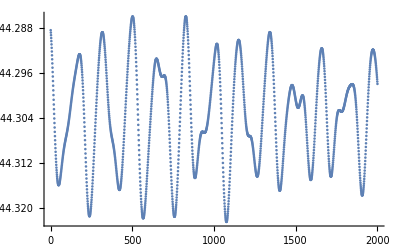

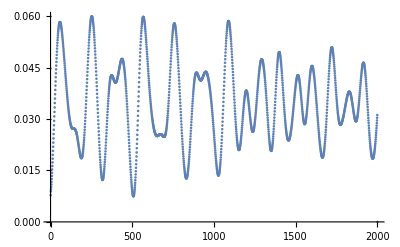

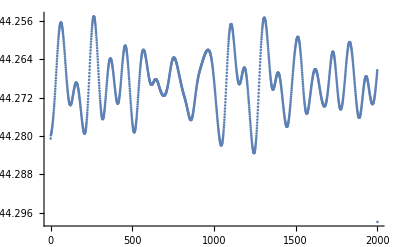

{{T→0.00178205}}

```mathematica
(*vou aquecer 5 vezes as particulas usando C1=1.2*)
(*vou arrefecer usando C1=0.5*)
C1=0.5;
Do[Do[velocity[[1,j,i]]=C1 velocity[[timesteps,j,i]],{i,1,3}],{j,1,13}]
Do[Do[position[[1,j,i]]=position[[timesteps,j,i]],{i,1,3}],{j,1,13}]

Do[force[[k,All,All]]=pairForceSum[ position[[k,All,All]] ];    energy[[k]] =pairEnergySum[ position[[k,All,All]]  ] ;kinetic[[k]] = 0.5  m  Sum[velocity[[k,j,i]]^2,{j,1,natoms},{i,1,3}];

(*Verlet Integration*)

If[k==1,position[[k+1,All,All]]=position[[k,All,All]]+dt velocity[[k,All,All]]+1/2 dt^2/m force[[k,All,All]]];
If[k≠1,position[[k+1,All,All]]=2 position[[k,All,All]]-position[[k-1,All,All]]+dt^2/m force[[k,All,All]];velocity[[k,All,All]]=(position[[k+1,All,All]]-position[[k-1,All,All]])/(2 dt)],{k,1,timesteps}]




energy[[timesteps+1]] =pairEnergySum[ position[[timesteps+1,All,All]]  ] ;
kinetic[[timesteps+1]] = 0.5  m  Sum[velocity[[timesteps+1,j,i]]^2,{j,1,natoms},{i,1,3}];
force[[timesteps+1,All,All]]=pairForceSum[ position[[timesteps+1,All,All]] ];
ListPlot[energy,PlotRange->All]
ListPlot[kinetic,PlotRange->All]
ListPlot[energy+kinetic,PlotRange->All]

averageKE=Sum[ dt kinetic[[i]],{i,1,timesteps}]/Sum[dt,{i,1,timesteps}];
Solve[averageKE==3/2 natoms kb T,T]
Animate[ListPointPlot3D[ position[[i,All,All]] ,BoxRatios->{1, 1, 1} ,PlotRange->All,PlotStyle->{PointSize[0.1]},PlotRangePadding->0.3,Axes->None,Boxed->False],{i,1,timesteps,1}]
```

## Temperatura obtida para transição do estado sólido para liquido→ Tliquid=T→0.25858eV

Set::write: Tag Rule in do estado gasoso obtida para^2 sólido Temperatura transição→Tliquid is Protected.

T→0.356028 eV

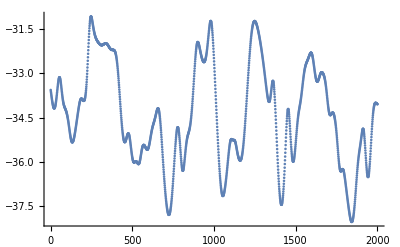

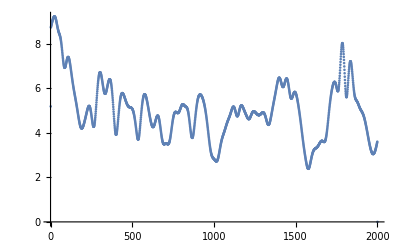

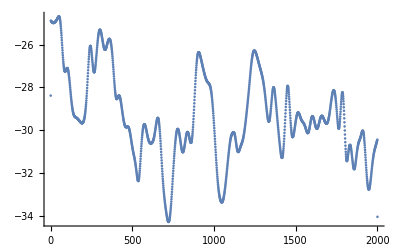

```mathematica
(*Gráficos para a temperatura de transição liquido*)
ListPlot[energy,PlotRange->All]
ListPlot[kinetic,PlotRange->All]
ListPlot[energy+kinetic,PlotRange->All]
```

### Arrefeci a temperatura até T =0.00178205 eV, encontrei a estrutura de um icosaedro pois é a estrutura que mais simétrica possível, que cancela as forças aplicadas, com um ponto no meio

```mathematica
(*Estas foram as energias encontradas*)
ListPlot[energy,PlotRange->All]
ListPlot[kinetic,PlotRange->All]
ListPlot[energy+kinetic,PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-